This code examines the variance and covariance of a very large swarm of robots as they  move inside a square workplace.
The swarm is large, but the robots are small in comparison, and together cover an area of constant volume A.
 When they are pushed to a side, they flow like water.
We want to know the mean position and variance of this swarm
Aaron T. Becker, Shiva Shahrokhi

It turns out (if the square is infinitely large) we can achieve any covairance. We cannot control the correlation:
correlation (X,Y) is
cor(X,Y) = (cov(X,Y))/(sd(X)*sd(Y))
For a right triangle aligned with the world axis, cor(X,Y) is 1/2 or -1/2.
And covariance is ±Area/18

todo:  as a function of α, determine the 8 regions of operation
plot the area for each region
solve for the mean in each region
solve for the variance and covariance for each region
make a plot of mean x,y as afunction of α and A
make a plot of covariance as a function of α and A
make a plot of variance as a function of α and A

Background Math Equations

The centroid (center of mass) = integral over A of x/Area

-Graphics-, g(x)  is the characteristic function (1 inside the region, 0 outside)

For a triangle, whose end points are L ={ x_L,y_L},M ={ x_M,y_M},N ={ x_N,y_N}

The centroid of a non-self-intersecting closed polygon defined by n vertices (x0,y0), (x1,y1), ..., (xn−1,yn−1) is the point (Cx, Cy), where

and where A is the polygon’s signed area,

## MonteCarlo Simulation This simulation shows that the correlation of a swarm of robots in a triangle is always ±1/2. The covariance is always ±Area/18

```mathematica
pts=RandomReal[{0,1},{100000,2}];
Manipulate[Module[{tpts,npts,cov,mean},
tpts =Select[ pts,#⟦1⟧≤ b-#⟦2⟧4 b^2&];
(*npts =Select[ pts,#⟦1⟧>b-#⟦2⟧4 b^2&];*)
cov =Covariance[tpts]; 
mean = Mean[tpts];
ListPlot[{(*npts,*)tpts},PlotMarkers->None,PlotStyle->{PointSize[Tiny]},PlotRange->{{-.2,1.2},{-.2,1.2}},AspectRatio->1,
PlotLabel->StringForm["Cov[xy]=``,Cor[XY]=``",cov⟦1,2⟧,cov⟦1,2⟧/(√(cov⟦1,1⟧)√(cov⟦2,2⟧))],Epilog->{Green,PointSize[Large],Point[mean],Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,6 cov]}]],{b,0.25,1}]
```

```mathematica
0 = m 1/(4b)+b  (*slope-intercept equation of a line for a triangle*)
-b 4 b = m 
a b = 1/4
a = 1/(4b)
```

```mathematica
rise = b, run =  1/(4b)
```

```mathematica
rise*run = 1/4
```

```mathematica
N[(1/8)/18]
```

0.00694444

## For α between 1/16 π to 7/16 π, what is the covariance?

```mathematica
xm =FullSimplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) xⅆy)ⅆx)/A]
FullSimplify[(0+2ell Cos[α])/3]
ym =FullSimplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) yⅆy)ⅆx)/A]
FullSimplify[(2*0+ell Sin[α])/3]
```

4/3 Cos[α] √(A Csc[2 α])

4/3 Cos[α] √(A Csc[2 α])

2/3 √(A Csc[2 α]) Sin[α]

2/3 √(A Csc[2 α]) Sin[α]

```mathematica
Clear[a]
∫_0^(b a) (∫_0^(x/b^2) yⅆy)ⅆx
(∫_0^(b a) (∫_0^(x/b^2) (y)ⅆy)ⅆx)
(∫_0^(b a) (∫_0^(x/b^2) (x )ⅆy)ⅆx )
```

a^3/(6 b)

a^3/(6 b)

(a^3 b)/3

### Compute covariance for a triangle with area 1/2 a^2 http : // www.talkstats.com/showthread.php/15046 - Uniform - distribution - on - a - triangle

```mathematica
Clear[a,b]
Simplify[(∫_0^(b a) (∫_0^(x/b^2) (x y)ⅆy)ⅆx)/(1/2 a^2)-(∫_0^(b a) (∫_0^(x/b^2) (x )ⅆy)ⅆx )/(1/2 a^2)(∫_0^(b a) (∫_0^(x/b^2) (y)ⅆy)ⅆx)/(1/2 a^2)]
Simplify[(∫_0^(b a) (∫_0^(x/b^2) (x )^2 ⅆy)ⅆx)/(1/2 a^2)-((∫_0^(b a) (∫_0^(x/b^2) (x )ⅆy)ⅆx )^2)/(1/2 a^2)]
Simplify[(∫_0^(b a) (∫_0^(x/b^2) (y )^2 ⅆy)ⅆx)/(1/2 a^2)-((∫_0^(b a) (∫_0^(x/b^2) (y )ⅆy)ⅆx )^2)/(1/2 a^2)]
```

a^2/36

1/18 a^2 (9-4 a^2) b^2

-(a^2 (-3+a^2))/(18 b^2)

```mathematica
Simplify[1/18 a^2 (9-4 a^2) b^2*-(a^2 (-3+a^2))/(18 b^2)]
```

1/324 a^4 (-3+a^2) (-9+4 a^2)

```mathematica
Clear[a]
FullSimplify[(a^2/36)/(√(1/18 a^2 (9-4 a^2) b^2)√((a^2 (-3+a^2))/(18 b^2)))]
```

a^2/(2 √((a^2 (-3+a^2))/b^2) √(a^2 (9-4 a^2) b^2))

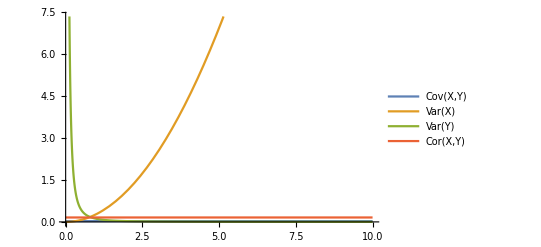

```mathematica
a=1;
Plot[{a^2/36,1/18 a^2 (9-4 a^2) b^2,-(a^2 (-3+a^2))/(18 b^2), (a^2/36)/(√(1/18 a^2 (9-4 a^2) b^2)√(-(a^2 (-3+a^2))/(18 b^2))) },{b,0,10},PlotLegends-> {"Cov(X,Y)","Var(X)","Var(Y)","Cor(X,Y)"}]
```

```mathematica
(*compute covariances.  Why is the covariance constant?  That doesn't make sense*)
Simplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) (x-4/3 Cos[α] √(A Csc[2 α]))^2 ⅆy)ⅆx)/A]
Simplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) (x)^2 ⅆy)ⅆx)/A-xm^2]
Simplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) (x y)ⅆy)ⅆx)/A-xm ym]
Simplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) (x-4/3 Cos[α] √(A Csc[2 α]))(y-2/3 √(A Csc[2 α]) Sin[α]) ⅆy)ⅆx)/A]
Simplify[ell =2 √(A Csc[2 α]);(∫_0^(ell Cos[α]) (∫_0^(Tan[α]x) (y)^2 ⅆy)ⅆx)/A-ym^2]
```

1/9 A Cot[α]

1/9 A Cot[α]

A/18

A/18

1/9 A Tan[α]

```mathematica
Simplify[A^2/2-8/9 A Cos[α] Csc[2 α] Sin[α]]
```

1/18 A (-8+9 A)

```mathematica
Manipulate[Module[{A = 1/8,ell ,mean,cov},
ell =2 √(A Csc[2 α]) (*=√((2A)/(Sin[α]Cos[α]))*);
mean={ (0+2ell Cos[α])/3,(2*0+ell Sin[α])/3};
cov ={{1/9 A^2 Cot[α],A^2/18},{A^2/18,1/9 A^2 Tan[α]}};
Plot[{If[x<ell Cos[α],Tan[α]x,0],A/(2 x)},{x,0,2},AspectRatio->1, Filling->{1->Axis,None},PlotRange->{{0,2},{0,2}},

Epilog->{Red,PointSize[Large],Point[mean],
Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,Sqrt[cov]],Ellipsoid[mean,2Sqrt[cov]]
},
PlotLabel->StringForm["Area = ``",1/2ell Cos[α]*Tan[α]ell Cos[α]]]],{α, 1/64 π , 15/32 π}]
```

```mathematica
Simplify[∫_0^1 (∫_0^x (x-xm)( y-ym)ⅆy)ⅆx]
Simplify[∫_0^1 (∫_0^x y yⅆy)ⅆx]
Simplify[∫_0^1 (∫_0^x x xⅆy)ⅆx]
```

1/24 (3-8 ym+4 xm (-1+3 ym))

1/12

1/4

```mathematica
Simplify[∫_cx^1 (∫_0^(cy/(1-cx)x-cy/(1-cx)cx) ⅆy)ⅆx]
Simplify[∫_cx^1 (∫_0^(cy/(1-cx)x-cy/(1-cx)cx) xⅆy)ⅆx]
```

```mathematica
Simplify[∫_cx^1 (∫_0^(cy/(1-cx)x-cy/(1-cx)cx) (x-(cx+2*1)/3)^2 ⅆy)ⅆx]
Simplify[∫_cx^1 (∫_0^(cy/(1-cx)x-cy/(1-cx)cx) (x-(cx+2*1)/3)(y-cy/3)ⅆy)ⅆx]
Simplify[∫_cx^1 (∫_0^(cy/(1-cx)x-cy/(1-cx)cx) (y-cy/3)^2 ⅆy)ⅆx]
```

-1/36 (-1+cx)^3 cy

1/72 (-1+cx)^2 cy^2

-1/36 (-1+cx) cy^3

```mathematica
Manipulate[ Module[{mean,cov,cxy,bwid=0.05,A},
A = (1-cx)cy/2;
mean ={ (cx+2*1)/3,cy/3};
cxy=1/72 (-1+cx)^2 cy^2;
cov ={{-1/36 (-1+cx)^3 cy,cxy},{cxy,-1/36 (-1+cx) cy^3}};
Plot[cy/(1-cx)x-cy/(1-cx)cx,{x,0,1},
PlotRange->{{-bwid,2+bwid},{-bwid,2+bwid}},AspectRatio->1,
PlotLabel->StringForm["Area = ``,mean=``, cov=``",A,mean,cov],
Prolog->{Darker[Red],Rectangle[{0,0}-bwid,{1,1}+bwid],White,Rectangle[{0,0},{1,1}]},
Epilog->{Red,PointSize[Large],Point[mean],Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,Sqrt[cov]],Ellipsoid[mean,2Sqrt[cov]]}


]],
{cx,0,0.99},{cy,0.01,1}]
```

```mathematica
Manipulate[ Module[{mean,cov,c,bwid=0.05,A},
A = Piecewise[{{1+(-1/2+b) Cot[α], b+Tan[α]≥1}, {1/2 (1+b Cot[α])^2 Tan[α], True}}];
mean = Piecewise[{{{-1/12 (-2-3 b+3 b^2+(4-3 b+3 b^2) Cos[2 α]) Csc[α]^2,1/6 (3+(-2+3 b) Cot[α])}, b+Tan[α]≥1}, {{1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α],1/6 (1+b Cot[α])^3 Tan[α]^2}, True}}];
c=Piecewise[{{{-1/12 (-2-3 b+3 b^2+(4-3 b+3 b^2) Cos[2 α]) Csc[α]^2,1/6 (3+(-2+3 b) Cot[α])}, b+Tan[α]≥1}, {{1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α],1/6 (1+b Cot[α])^3 Tan[α]^2,Cot[α]/12+1/3 (1+(-1+b) Cot[α])}, True}}];
cov ={{c⟦1⟧,c⟦2⟧},{c⟦2⟧,c⟦3⟧}};
RegionPlot[y-Tan[α]x<b,{x,0,1},{y,0,1},PlotLabel->StringForm["Area = ``,``",A,mean],
PlotRange->{{-bwid,1+bwid},{-bwid,1+bwid}},
Prolog->{Opacity[0],EdgeForm[{Thick,Red}],Point[mean]},
Epilog->{Darker[Red],Rectangle[{0,0}-bwid,{1,1}+bwid],White,Rectangle[{0,0},{1,1}]}

]],
{α,0.01,π/2},{b,-1,1}]
```

## Calculate the Area for triangle beyond line y=Tan[α]x + b

```mathematica
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 ∫_0^(Tan[α]x + b) ⅆyⅆx]]
```

1/2 (1+b Cot[α])^2 Tan[α]

```mathematica
Assuming[b<0 &&α>0&& α<π/2,

∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 ⅆyⅆx
]
```

1+Cot[α]/2-(1-b) Cot[α]

```mathematica
Simplify[If[Tan[α]+b<1,b+b^2 Cot[α]-1/2 b^2 Csc[α] Sec[α]+Tan[α]/2+1/2 b^2 Tan[α], 1+Cot[α]/2-(1-b) Cot[α]]]
```

Piecewise[{{1+(-1/2+b) Cot[α], b+Tan[α]≥1}, {1/2 (1+b Cot[α])^2 Tan[α], True}}]

## Calculate the Mean for triangle beyond line Tan[α]x + b

```mathematica
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 ∫_0^(Tan[α]x + b) xⅆyⅆx]]
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 ∫_0^(Tan[α]x + b) yⅆyⅆx]]
```

1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α]

1/6 (1+b Cot[α])^3 Tan[α]^2

```mathematica
Assuming[b<0 &&α>0&& α<π/2,

∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) x ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 x ⅆyⅆx
]
Assuming[b<0 &&α>0&& α<π/2,

∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) y ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 y ⅆyⅆx
]
```

Cot[α]^2/3-1/2 b Cot[α]^2+1/2 (2+(-2+b) b-(-1+b)^2 Csc[α]^2)

Cot[α]/6+1/2 (1+(-1+b) Cot[α])

```mathematica
Simplify[If[Tan[α]+b<1,{1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α],1/6 (1+b Cot[α])^3 Tan[α]^2}
,{Cot[α]^2/3-1/2 b Cot[α]^2+1/2 (2+(-2+b) b-(-1+b)^2 Csc[α]^2),Cot[α]/6+1/2 (1+(-1+b) Cot[α])}]]
```

Piecewise[{{{-1/12 (-2-3 b+3 b^2+(4-3 b+3 b^2) Cos[2 α]) Csc[α]^2,1/6 (3+(-2+3 b) Cot[α])}, b+Tan[α]≥1}, {{1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α],1/6 (1+b Cot[α])^3 Tan[α]^2}, True}}]

## Calculate the Variance for triangle beyond line Tan[α]x + b

```mathematica
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 (x^2∫_0^(Tan[α]x + b) ⅆy)ⅆx]]
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 ∫_0^(Tan[α]x + b) y^2 ⅆyⅆx]]
Simplify[Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^1 (x∫_0^(Tan[α]x + b) yⅆy)ⅆx]]
```

1/12 (3+4 b Cot[α]+b^4 Cot[α]^4) Tan[α]

1/12 (1+b Cot[α])^4 Tan[α]^3

-1/6 Csc[2 α]^2 (b Cos[α]-3 Sin[α]) (b Cos[α]+Sin[α])^3

```mathematica
Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) x^2 ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 x^2 ⅆyⅆx]
Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) x y ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 x y ⅆyⅆx]
Assuming[b<0 &&α>0&& α<π/2,∫_(-b/ Tan[α])^((1-b)/ Tan[α]) ∫_0^(Tan[α]x + b) y^2 ⅆyⅆx + ∫_((1-b)/ Tan[α])^1 ∫_0^1 y^2  ⅆyⅆx]
```

Cot[α]^3/4-2/3 b Cot[α]^3+1/2 b^2 Cot[α]^3+1/6 (1+(-1+b) Cot[α]) Csc[α]^2 (2+(-2+b) b+(-2+b) b Cos[2 α]-(-1+b) Sin[2 α])

1/24 (3-4 b) Cot[α]^2+1/4 (2+(-2+b) b-(-1+b)^2 Csc[α]^2)

Cot[α]/12+1/3 (1+(-1+b) Cot[α])

```mathematica
Simplify[If[Tan[α]+b<1,{1/12 (3+4 b Cot[α]+b^4 Cot[α]^4) Tan[α],1/12 (1+b Cot[α])^4 Tan[α]^3,-1/6 Csc[2 α]^2 (b Cos[α]-3 Sin[α]) (b Cos[α]+Sin[α])^3}
,{Cot[α]^3/4-2/3 b Cot[α]^3+1/2 b^2 Cot[α]^3+1/6 (1+(-1+b) Cot[α]) Csc[α]^2 (2+(-2+b) b+(-2+b) b Cos[2 α]-(-1+b) Sin[2 α]),1/24 (3-4 b) Cot[α]^2+1/4 (2+(-2+b) b-(-1+b)^2 Csc[α]^2),}]]
```

```mathematica
Piecewise[{{{-1/12 (-2-3 b+3 b^2+(4-3 b+3 b^2) Cos[2 α]) Csc[α]^2,1/6 (3+(-2+3 b) Cot[α])}, b+Tan[α]≥1}, {{1/6 (2+3 b Cot[α]-b^3 Cot[α]^3) Tan[α],1/6 (1+b Cot[α])^3 Tan[α]^2,Cot[α]/12+1/3 (1+(-1+b) Cot[α])}, True}}]
```

## Line is y = Tan[θ]x+ 1-A-Tan[θ]/2

Set::setraw: Cannot assign to raw object 1.

```mathematica
(*Plot a constant area place denoted by θ*)
Manipulate[Module[{L=1,θ = ArcTan[-pDir⟦2⟧,pDir⟦1⟧]},

Graphics[{ White, Rectangle[1.05{1,1},1.05{1,1}],Darker[Red], Rectangle[-1.025{1,1},1.025{1,1}],White, Rectangle[{-1,-1},{1,1}],
Blue,Line[{{0,0},pDir}],
Red,Line[{pDir+{-pDir⟦2⟧,pDir⟦1⟧},pDir+{pDir[[2]],-pDir[[1]]}}],
Orange, Line[{{0,1-A-Tan[θ]/2},{1, Tan[θ]+1-A-Tan[θ]/2}}],
 Line[{{0,1-A-Tan[θ]/2},{-1, -Tan[θ]+1-A-Tan[θ]/2}}],
Green, Line[{{0,1-A/2-Tan[θ]/2},{1, Tan[θ]+1-A/2-Tan[θ]/2}}],
 Line[{{0,1-A/2-Tan[θ]/2},{-1, -Tan[θ]+1-A/2-Tan[θ]/2}}]


},PlotRange->{1.025{-1,1},1.025{-1,1}}
]
],{{pDir,{2/3,1/4}},{-1,-1},{1,1},Locator},{{A,1/2},1/100,1}
]
```

### Try a different Way

```mathematica
A=1/8
N[Tan[2A] ]
N[Tan[1/(2 A)] ]
```

1/8

0.255342

1.15782

```mathematica
(*Plot a constant area place denoted by θ*)
Manipulate[Module[{L=1/2,bw=1/20,α=π/2+θ, el,A=1/8},
el =√((2 A)/(Cos[α]Sin[α]));
Graphics[{ White, Rectangle[1.05{L,L},1.05{L,L}],
Blue,HalfPlane[{{0,0},{Sin[θ],-Cos[θ]}},{Cos[θ],Sin[θ]}],
Green,
HalfPlane[{{L-el Cos[α],-L},{L,-L+el Sin[α]}},{Cos[θ],Sin[θ]}],
(*borders*)
Darker[Red],
 Rectangle[{-(L+bw),-(L+bw)},{(L+bw),-(L)}],
 Rectangle[{-(L+bw),-(L+bw)},{-L,(L+bw)}],
 Rectangle[{(L),(L+bw)},{-L,L}],
Rectangle[{(L),-(L)},{L+bw,L+bw}],
Text[StringForm["alpha = ``",α],{0,1/4}]

},PlotRange->{1.025{-L,L},1.025{-L,L}}
]
],{θ,-π/2,3/2π}
]
```

```mathematica
Cos[α+π/2]
```

-Sin[α]